```mathematica
Needs["Splines`"]
randomizedTube[r1_,r2_,s_,lvls_,d_]:=Module[{ints,bz},
ints = Table[r1+(r2-r1)/lvls*i+{RandomVariate[NormalDistribution[0,d]],RandomVariate[NormalDistribution[0,d]],0},{i,1,lvls-1}];
ints=Join[{r1},ints,{r2}];
bz=BezierCurve[ints];
(*Graphics3D[{Tube[bz,s],Tube[{r1,r2},s]}]*)
Tube[bz,s]
];
```

```mathematica
cm=72/2.54;
(* custom eigensystem *)
Clear[orderedEigensystem]
orderedEigensystem[M_,f_:Re]:=Module[{eigsys, order},
eigsys = Eigensystem[M];
order = Ordering[f[eigsys[[1]]]];
{eigsys[[1,order]],eigsys[[2,order]]ᵀ}
];

(* compute density of states *)
Clear[DOS]
DOS[E_,NE_]:=Module[{min,max,Eints,dos},
{min,max}=MinMax[E];
Eints =min+ Table[(max-min)/NE n,{n,0,NE}];
dos=Table[Length[Nearest[E,e,{Infinity,(max-min)/(2*NE)}]],{e,Eints}];
(*Print[Eints,Length[E]];*)
{Eints,dos/Length[E]}ᵀ
];

(* custom eigensystem *)
Clear[orderedGaugedEigensystem]
orderedGaugedEigensystem[M_,f_:Re]:=Module[{vals,vecs, order,phase,phasemod},
{vals,vecs} = Eigensystem[M];
order = Ordering[f[vals]];
vals=vals[[order]];
vecs=vecs[[order]];
phase = Arg[vecs[[1,1]]];
vecs/=Exp[ⅈ*(phase)];
vecs=vecsᵀ;
{vals,vecs}
];
Clear[regauge]
regauge[v1_,v2_]:=Module[{p1,p1m,p2,p1s,p1f,vf},
p1 = Arg[v1[[1,1]]];
p1m = Mod[p1,2π];
p2 = Arg[v2[[1,1]]];
p1s = Table[p1m+n π,{n,-2,2}];
p1f=Nearest[p1s,Mod[p2,2π]][[1]];
(*Print[StringForm["p_1=`1`, p_2=`2`, p_1/π=`3`, p_(1, f)=`4`",p1, p2,(p1-p2)/π,p1f]];*)
vf =v1* ⅇ^(-ⅈ (p1 - p1f))
];

Clear[Fk,Norb,x,y,Fx,u,ux,Fx, nestedWilsonLoopxky,res,Norb]
nestedWilsonLoopxky[Norb_,res_]:=Module[{Wtilde, W,Wxy,udu,Vxy,Axy,Fxy,phase,prod,ux,u,vals,vecs,vs,Lx,Ly,tr},
{Lx,Ly,tr}=Dimensions[res];
Wtilde={};
W = ConstantArray[0,{Lx,Ly,2,2}];
udu = ConstantArray[0,{Lx,Ly,Norb,tr-Norb}];
Do[
Wxy={};
Vxy={};
Axy={};
Do[
Fxy = IdentityMatrix[Norb];
phase=1;
Do[
u=res[[Mod[x+xp-1,Lx]+1,y,3,2,;;,;;Norb]];
ux=res[[Mod[x+xp,Lx]+1,y,3,2,;;,;;Norb]];
prod = ux†.u;
If[xp==0,udu[[x,y]]=prod];
Fxy=prod.Fxy;
Fxy/=Norm[Fxy]; (* this might stabilize *)
,{x,1,Lx}];
{vals,vecs} = orderedGaugedEigensystem[Fxy,Im];
AppendTo[Wxy,Table[Arg[e]/(2π),{e,vals}]];
AppendTo[Axy,Table[Abs[e],{e,vals}]];
vs=res[[Mod[xp,Lx]+1,y,3,2,;;,;;Norb]].vecs;
If[Vxy≠{}, vs = regauge[vs,Vxy[[-1]]];];
AppendTo[Vxy,vs];
W[[xp+1,y]]=prod;
,{y,1,Ly}];
AppendTo[Wtilde,Eigenvalues[Chop[Product[Vxy[[Mod[n,Length[kys]]+1]]†.Vxy[[n]],{n,Length[kys]}]]]];
,{xp,0,Lx-1}];
{Wxy,Wtilde,Vxy,udu}
]

nestedWilsonLoopykx[Norb_,res_]:=Module[{Wtilde, W,Wxy,udu,Vxy,Axy,Fxy,phase,prod,ux,u,vals,vecs,vs,Lx,Ly,tr},
{Lx,Ly,tr}=Dimensions[res];
Wtilde={};
W = ConstantArray[0,{Lx,Ly,Norb,tr-Norb}];
udu = ConstantArray[0,{Lx,Ly,Norb,tr-Norb}];
Do[
Wxy={};
Vxy={};
Axy={};
Do[
Fxy = IdentityMatrix[Norb];
phase=1;
Do[
u=res[[x,Mod[y+yp-1,Ly]+1,3,2,;;,;;Norb]];
ux=res[[x,Mod[y+yp,Ly]+1,3,2,;;,;;Norb]];
prod = ux†.u;
If[yp==0,udu[[x,y]]=prod];
Fxy=prod.Fxy;
Fxy/=Norm[Fxy]; (* this might stabilize *)
,{y,1,Ly}];
{vals,vecs} = orderedGaugedEigensystem[Fxy,Im];
AppendTo[Wxy,Table[Arg[e]/(2π),{e,vals}]];
AppendTo[Axy,Table[Abs[e],{e,vals}]];
vs=res[[x,Mod[yp,Ly]+1,3,2,;;,;;Norb]].vecs;
If[Vxy≠{}, vs = regauge[vs,Vxy[[-1]]];];
AppendTo[Vxy,vs];
W[[x,yp+1]]=prod;
,{x,1,Lx}];
AppendTo[Wtilde,Eigenvalues[Chop[Product[Vxy[[Mod[n,Length[kys]]+1]]†.Vxy[[n]],{n,Length[kys]}]]]];
,{yp,0,Ly-1}];
{Wxy,Wtilde,Vxy,udu}
]
```

```mathematica
(PauliMatrix[1]+ⅈ PauliMatrix[2])/2
(PauliMatrix[1]-ⅈ PauliMatrix[2])/2
```

{{0,1},{0,0}}

{{0,0},{1,0}}

```mathematica
Σ[i_,j_]:=KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]
ℍ[kx_,ky_,Σ_]:=(γx+λx Cos[kx])Σ[1,0]-(γy+λy Cos[ky])Σ[2,2]- λx*Cos[kx+ϕx]Σ[2,3]-λy Cos[ky+ϕy]Σ[2,1]
```

```mathematica
Table[DeleteDuplicates[Flatten[ℍ[kx,ky,Σ].Σ[i,j]+Σ[i,j].ℍ[kx,ky,Σ]]]//Length,{i,0,3},{j,0,3}]
ℍ[kx,ky,Σ].Σ[3,0]+Σ[3,0].ℍ[kx,ky,Σ]//DeleteDuplicates
```

{{7,4,5,5},{2,5,7,7},{5,3,2,6},{1,5,6,3}}

{{0,0,0,0}}

```mathematica
Lx=100;Ly=100;
kxs =N[ Table[(2π)/Lx i-π,{i,Lx}]];
kys =N[ Table[(2π)/Ly i-π,{i,Ly}]];
res=Table[{kx,ky,orderedEigensystem[N[ℍ[kx,ky,Σ]]/.{γx->0.,γy->0.2,λx->1,λy->1,ϕx->0π/2,ϕy->0π/2}]},{kx,kxs},{ky,kys}];
spec=Flatten[res,1];
bands=Table[{s[[1]],s[[2]], ev},{s,spec}, {ev,s[[3,1]]}]ᵀ;
```

```mathematica
ListPlot3D[Table[b,{b,bands}],PlotTheme->"Scientific"]
```

-Graphics3D-

```mathematica
Clear[δ,fourierTransform]
δ[x_,y_]=If[x==y,1,0];
delt[t_]:=(δ[Simplify[-I t],0]/.{kx-> 1,ky-> 0}) (δ[Simplify[-I t],0]/.{kx-> 0,ky-> 1});
fourierTransform[ham_,lx_,ly_]:=Module[{Hrs,Hfull},

Hrs[x1_,x2_,y1_,y2_]=(ham*Exp[ⅈ*{kx,ky}.({x1,y1}-{x2,y2})]//TrigToExp//ExpandAll)/.E^sym_-> g[sym]/.{g->delt};
Print[Hrs[x1,x2,y1,y2]];
(* assign local real space Hamiltonian *)
(* now construct the full one *)
Hfull= ConstantArray[0,{lx,ly,4,lx,ly,4}];
Do[
If[x1>0&&x1≤lx&&y2>0&&y2≤ly,
Hfull[[x1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];

,{x1,x2-5,x2+5},{x2,lx},{y1,ly},{y2,y1-5,y1+5}];
ArrayReshape[Hfull,{lx*ly*4,lx*ly*4}]
];
```

```mathematica
ℍrs = fourierTransform[ℍ[kx,ky,Σ]/.{ϕx->π/4,ϕy->π/4},16,8];
```

{{0,0,1/2 λx If[-1+x1-x2==0,1,0] If[y1-y2==0,1,0]+γx If[x1-x2==0,1,0] If[y1-y2==0,1,0]+1/2 λx If[1+x1-x2==0,1,0] If[y1-y2==0,1,0]+1/2 ⅈ λx If[-1-π/4+x1-x2==0,1,0] If[-π/4+y1-y2==0,1,0]+1/2 ⅈ λx If[1+π/4+x1-x2==0,1,0] If[π/4+y1-y2==0,1,0],1/2 λy If[x1-x2==0,1,0] If[-1+y1-y2==0,1,0]+γy If[x1-x2==0,1,0] If[y1-y2==0,1,0]+1/2 λy If[x1-x2==0,1,0] If[1+y1-y2==0,1,0]+1/2 ⅈ λy If[-π/4+x1-x2==0,1,0] If[-1-π/4+y1-y2==0,1,0]+1/2 ⅈ λy If[π/4+x1-x2==0,1,0] If[1+π/4+y1-y2==0,1,0]},{0,0,-1/2 λy If[x1-x2==0,1,0] If[-1+y1-y2==0,1,0]-γy If[x1-x2==0,1,0] If[y1-y2==0,1,0]-1/2 λy If[x1-x2==0,1,0] If[1+y1-y2==0,1,0]+1/2 ⅈ λy If[-π/4+x1-x2==0,1,0] If[-1-π/4+y1-y2==0,1,0]+1/2 ⅈ λy If[π/4+x1-x2==0,1,0] If[1+π/4+y1-y2==0,1,0],1/2 λx If[-1+x1-x2==0,1,0] If[y1-y2==0,1,0]+γx If[x1-x2==0,1,0] If[y1-y2==0,1,0]+1/2 λx If[1+x1-x2==0,1,0] If[y1-y2==0,1,0]-1/2 ⅈ λx If[-1-π/4+x1-x2==0,1,0] If[-π/4+y1-y2==0,1,0]-1/2 ⅈ λx If[1+π/4+x1-x2==0,1,0] If[π/4+y1-y2==0,1,0]},{1/2 λx If[-1+x1-x2==0,1,0] If[y1-y2==0,1,0]+γx If[x1-x2==0,1,0] If[y1-y2==0,1,0]+1/2 λx If[1+x1-x2==0,1,0] If[y1-y2==0,1,0]-1/2 ⅈ λx If[-1-π/4+x1-x2==0,1,0] If[-π/4+y1-y2==0,1,0]-1/2 ⅈ λx If[1+π/4+x1-x2==0,1,0] If[π/4+y1-y2==0,1,0],-1/2 λy If[x1-x2==0,1,0] If[-1+y1-y2==0,1,0]-γy If[x1-x2==0,1,0] If[y1-y2==0,1,0]-1/2 λy If[x1-x2==0,1,0] If[1+y1-y2==0,1,0]-1/2 ⅈ λy If[-π/4+x1-x2==0,1,0] If[-1-π/4+y1-y2==0,1,0]-1/2 ⅈ λy If[π/4+x1-x2==0,1,0] If[1+π/4+y1-y2==0,1,0],0,0},{1/2 λy If[x1-x2==0,1,0] If[-1+y1-y2==0,1,0]+γy If[x1-x2==0,1,0] If[y1-y2==0,1,0]+1/2 λy If[x1-x2==0,1,0] If[1+y1-y2==0,1,0]-1/2 ⅈ λy If[-π/4+x1-x2==0,1,0] If[-1-π/4+y1-y2==0,1,0]-1/2 ⅈ λy If[π/4+x1-x2==0,1,0] If[1+π/4+y1-y2==0,1,0],1/2 λx If[-1+x1-x2==0,1,0] If[y1-y2==0,1,0]+γx If[x1-x2==0,1,0] If[y1-y2==0,1,0]+1/2 λx If[1+x1-x2==0,1,0] If[y1-y2==0,1,0]+1/2 ⅈ λx If[-1-π/4+x1-x2==0,1,0] If[-π/4+y1-y2==0,1,0]+1/2 ⅈ λx If[1+π/4+x1-x2==0,1,0] If[π/4+y1-y2==0,1,0],0,0}}

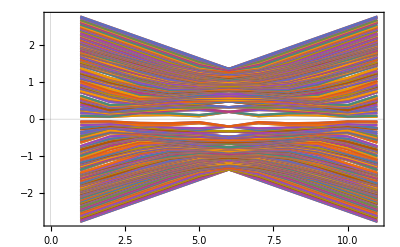

```mathematica
ListPlot[Table[Eigenvalues[N[ℍrs/.{γx->g, γy->g,λx->1, λy->1}]]//Sort,{g,-1,1,0.2}]ᵀ,PlotTheme->"Scientific",Joined->True]
```

```mathematica
L=9
lx=L;ly=L;
ℍos= ConstantArray[0,{lx,ly,4,lx,ly,4}];
Do[
ℍos[[x,y,2,x,y,1]]+=γx1;
ℍos[[x,y,4,x,y,3]]+=γx2;
ℍos[[x,y,3,x,y,2]]+=γy1;
ℍos[[x,y,1,x,y,4]]+=γy2;
,{x,lx},{y,ly}];
ℍnn= ConstantArray[0,{lx,ly,4,lx,ly,4}];
Do[
ℍnn[[x+1,y,4,x,y,3]]+=λx1;
ℍnn[[x,y,2,x+1,y,1]]+=λx2;
,{x,lx-1},{y,ly}];
Do[
ℍnn[[x,y+1,1,x,y,4]]+=λy1;
ℍnn[[x,y,3,x,y+1,2]]+=λy2;
,{x,lx},{y,ly-1}];
Hrs=ArrayReshape[ℍos+ℍnn,{lx*ly*4,lx*ly*4}];
Hrs=Hrs+Hrs†;
gs=Table[g,{g,-2,2,0.025}];
red=RGBColor[152/255,30/255,20/255];
```

9

```mathematica
<<MaTeX`
Monitor[
spec1=Table[Sort[Eigenvalues[Hrs/.{γx1->g ⅇ^(ⅈ π/2),γx2->g,γy1->g,γy2->g,λx1->1,λx2->1,λy1->ⅇ^(ⅈ π/2),λy2->1}]],{g,gs}];,g]
```

```mathematica
tns=Thickness[0.005];Clear[tickFunc]
tickFunc=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.05,.025}][##]&;
```

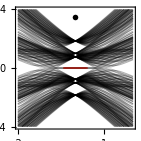

```mathematica
sl=60;
inset1=ListPlot[spec1ᵀ[[2 L^2-1;;2 L^2+2,sl;;-sl]],DataRange->{gs[[sl]],gs[[-sl]]},PlotStyle->Directive[red,tns],Joined->True];
p1= Show[ListPlot[spec1ᵀ,Joined->True,GridLines->None,PlotTheme->"Scientific",PlotRange->{-4,4},PlotRangePadding->0,DataRange->{-2,2},AspectRatio->1,ImageSize->5cm,FrameLabel->MaTeX[{"g","\\varepsilon"}],FrameStyle->Directive[Thin,Black],PlotStyle->Directive[tns,Black, Opacity[0.3]],FrameTicks->{{tickFunc,None},{tickFunc,None}}],inset1,Epilog->Inset[MaTeX["(a)"],{0,3.5},{Center,Center}]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["BBH.jpg",p1,ImageResolution->600]
```

/Users/andreashaller/mathematica_files

BBH.jpg

```mathematica
<<MaTeX`
Monitor[
spec2=Table[Sort[Eigenvalues[Hrs/.{γx1->g ⅇ^(ⅈ π/2),γx2->g,γy1->g,γy2->g,λx1->1,λx2->1.5,λy1->1.5 ⅇ^(ⅈ π/2),λy2->1}]],{g,gs}];,g]
```

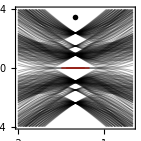

```mathematica
sl=60;tns=Thickness[0.005];
inset2=ListPlot[spec2ᵀ[[2 L^2-1;;2 L^2+2,sl;;-sl]],DataRange->{gs[[sl]],gs[[-sl]]},PlotStyle->Directive[red,tns],Joined->True];
p2= Show[ListPlot[spec2ᵀ,Joined->True,GridLines->None,PlotTheme->"Scientific",PlotRange->{-4,4},PlotRangePadding->0,DataRange->{-2,2},AspectRatio->1,ImageSize->5cm,FrameLabel->MaTeX[{"g","\\varepsilon"}],FrameStyle->Directive[Thin,Black],PlotStyle->Directive[tns,Black, Opacity[0.3]],FrameTicks->{{tickFunc,None},{tickFunc,None}}],inset2,Epilog->Inset[MaTeX["(b)"],{0,3.5},{Center,Center}]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["BBH_broken_mirrors.jpg",p2,ImageResolution->600]
```

/Users/andreashaller/mathematica_files

BBH_broken_mirrors.jpg

```mathematica
L=3
lx=L;ly=L;
ℍos= ConstantArray[0,{lx,ly,4,lx,ly,4}];
Do[
ℍos[[x,y,2,x,y,1]]+=γx1;
ℍos[[x,y,4,x,y,3]]+=γx2;
ℍos[[x,y,3,x,y,2]]+=γy2;
ℍos[[x,y,1,x,y,4]]+=γy1;
,{x,lx},{y,ly}];
ℍnn= ConstantArray[0,{lx,ly,4,lx,ly,4}];
Do[
ℍnn[[x+1,y,4,x,y,3]]+=λx1;
ℍnn[[x,y,2,x+1,y,1]]+=λx2;
,{x,lx-1},{y,ly}];
Do[
ℍnn[[x,y+1,1,x,y,4]]+=λy1;
ℍnn[[x,y,3,x,y+1,2]]+=λy2;
,{x,lx},{y,ly-1}];
Hrs=ArrayReshape[ℍos+ℍnn,{lx*ly*4,lx*ly*4}];
Hrs=Hrs+Hrs†;
<<MaTeX`
gs=Table[g,{g,-2,2,0.025}];
red=RGBColor[152/255,30/255,20/255];
gsel = 0.4;fs=28;
Hlatt=ArrayReshape[Hrs/.{γx1->gsel ⅇ^(ⅈ π/2),γx2->gsel,γy1->gsel,γy2->gsel,λx1->1,λx2->1.5,λy1->1.5 ⅇ^(ⅈ π/2),λy2->1},{lx,ly,4,lx,ly,4}];
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Abs[Arg[Hlatt//Flatten]]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}]
ucd=.2;
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};sublatt = sublatt[[{1,2,3,4}]];
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Line[{#[[1]]-{0,0.125,0},#[[1]]-{0,0.225,0}}],Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->fs],#[[1]]]}&/@{{{2,2.425,0},"x,1"},{{2,2.025,0},"x,2"},{{1.6,1.025,0},"y,1"},{{2.0,1.025,0},"y,2"}};
lbl2={Line[{#[[1]]+#[[3]],#[[1]]+#[[4]]}],Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->fs],#[[1]]]}&/@{{{2.5,2.4,0},"x,1",{0.175,0,0},{0.3,0,0}},{{2.5,2,0},"x,2",{0.175,0,0},{0.3,0,0}},{{1.5,1.5,0},"y,1",{0.175,0,0},{0.3,0,0}},{{2.5,1.5,0},"y,2",-{0.175,0,0},-{0.3,0,0}}};
sps =Table[{n,0.1},{n,latt}];
p3=Graphics3D[Join[lbl1,lbl2,{Black,Sphere[#,0.1]}&/@latt,{{cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],Tube[{#[[1]],#[[2]]},#[[3,1]]*0.03]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic",Boxed->False]
```

3

ColorDataFunction[…]

{0,1.5708}

{RGBColor[0.9584254999999999, 0.877884, 0.5906629999999999],RGBColor[0.431296, 0.709773, 0.927077]}

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["BBH_symm_broken.jpg",p3,ImageResolution->600]
```

/Users/andreashaller/mathematica_files

BBH_symm_broken.jpg

```mathematica
gsel = 0.4
Hlatt=ArrayReshape[Hrs/.{γx1->gsel ⅇ^(ⅈ π/4),γx2->gsel ⅇ^(ⅈ π/4),γy1->gsel,γy2->gsel,λx1->1.0,λx2->1.0,λy1->1. ⅇ^(ⅈ π/4),λy2->1.0 ⅇ^(ⅈ π/4)},{lx,ly,4,lx,ly,4}];
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Abs[Arg[Hlatt//Flatten]]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}]
ucd=.2;
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
sps =Table[{n,0.1},{n,latt}];
p4=Graphics3D[Join[lbl1,lbl2,{Black,Sphere[#,0.1]}&/@latt,{{cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],Tube[{#[[1]],#[[2]]},#[[3,1]]*0.03]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic",Boxed->False]
```

0.4

ColorDataFunction[…]

{0,0.785398}

{RGBColor[0.9584254999999999, 0.877884, 0.5906629999999999],RGBColor[0.431296, 0.709773, 0.927077]}

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["BBH_symm.jpg",p4,ImageResolution->600]
```

/Users/andreashaller/mathematica_files

BBH_symm.jpg

```mathematica
gsel = 0.
Hlatt=ArrayReshape[Hrs/.{γx1->gsel,γx2->gsel,γy1->gsel,γy2->gsel,λx1->1.0,λx2->1.0,λy1->1.,λy2->1.0},{lx,ly,4,lx,ly,4}];
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Abs[Arg[Hlatt//Flatten]]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}];
cols={cfun[0.5]};
ucd=.2;
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
latt1=latt;
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2,2.3,0},"x,1"},{{2,1.9,0},"x,2"},{{1.65,2.05,0},"y,1"},{{2.05,2.05,0},"y,2"}}};
lbl2={Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2.5,2.3,0},"x,1"},{{2.5,1.9,0},"x,2"},{{1.65,2.5,0},"y,1"},{{2.05,2.5,0},"y,2"}}};
sps =Table[{n,0.1},{n,latt}];

bl1=Graphics3D[Join[{Black,Sphere[#,0.1]}&/@latt,{{cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],Tube[{#[[1]],#[[2]]},#[[3,1]]*0.03]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic"];

latt = Flatten[Table[{x,y,1}+b,{x,lx},{y,ly},{b,sublatt}],2];
latt2=latt;
conn = Flatten[Table[{{x1,y1,1}+sublatt[[b1]],{x2,y2,1}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2,2.3,0},"x,1"},{{2,1.9,0},"x,2"},{{1.65,2.05,0},"y,1"},{{2.05,2.05,0},"y,2"}}};
lbl2={Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2.5,2.3,0},"x,1"},{{2.5,1.9,0},"x,2"},{{1.65,2.5,0},"y,1"},{{2.05,2.5,0},"y,2"}}};
sps =Table[{n,0.1},{n,latt}];
bl2=Graphics3D[Join[{Black,Sphere[#,0.1]}&/@latt,{{cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],Tube[{#[[1]],#[[2]]},#[[3,1]]*0.03]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic"];
```

0.

ColorDataFunction[…]

{0}

```mathematica
inodes=Table[{2,2,0}+b,{b,{0,1,0}}]
int=Graphics3D[{cfun[0],Opacity[0.3],EdgeForm[None],Tube[{#,#+{0,0,1}},.07]}&/@latt]
```

{{2,2,0},{3,3,1},{2,2,0}}

-Graphics3D-

```mathematica
inodes=Table[{2,2,0}+b,{b,sublatt}]
int=Graphics3D[{cfun[0],Opacity[0.3],EdgeForm[None],Tube[{#,#+{0,0,1}},.07]}&/@latt]
```

{{1.8,1.8,0.},{2.2,1.8,0.},{2.2,2.2,0.},{1.8,2.2,0.}}

-Graphics3D-

```mathematica
p=Show[bl1,bl2,Graphics3D[{Text[MaTeX["s=\\uparrow"],{2.75,0,1}],Text[MaTeX["s=\\downarrow"],{2.75,0,0}]}],int,ViewPoint->{π/4,π/2,π/7},Boxed->False]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["H1.jpg",p,ImageResolution->600]
```

H1.jpg

```mathematica
gsel = 0.
Hlatt=ArrayReshape[Hrs/.{γx1->gsel,γx2->gsel,γy1->gsel,γy2->gsel,λx1->1.0,λx2->1.0,λy1->1.,λy2->1.0},{lx,ly,4,lx,ly,4}];
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Abs[Arg[Hlatt//Flatten]]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}];
cols={Gray};
ucd=.2;
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
latt1=latt;
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2,2.3,0},"x,1"},{{2,1.9,0},"x,2"},{{1.65,2.05,0},"y,1"},{{2.05,2.05,0},"y,2"}}};
lbl2={Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2.5,2.3,0},"x,1"},{{2.5,1.9,0},"x,2"},{{1.65,2.5,0},"y,1"},{{2.05,2.5,0},"y,2"}}};
sps =Table[{n,0.1},{n,latt}];

latt=Graphics3D[Join[{Black,Sphere[#,0.1]}&/@latt,{{cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],Tube[{#[[1]],#[[2]]},#[[3,1]]*0.03]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic"]
```

0.

ColorDataFunction[…]

{0}

-Graphics3D-

```mathematica
gsel=1;lsel=0;
Hlatt=ArrayReshape[Hrs/.{γx1->gsel,γx2->gsel,γy1->gsel,γy2->gsel,λx1->lsel,λx2->lsel,λy1->lsel,λy2->lsel},{lx,ly,4,lx,ly,4}];
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Abs[Arg[Hlatt//Flatten]]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}];
cols={cfun[1]};
ucd=.2;
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
latt1=latt;
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2,2.3,0},"x,1"},{{2,1.9,0},"x,2"},{{1.65,2.05,0},"y,1"},{{2.05,2.05,0},"y,2"}}};
lbl2={Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2.5,2.3,0},"x,1"},{{2.5,1.9,0},"x,2"},{{1.65,2.5,0},"y,1"},{{2.05,2.5,0},"y,2"}}};
sps =Table[{n,0.1},{n,latt}];

latt1=Graphics3D[Join[{Black,Sphere[#,0.1]}&/@latt,{{Opacity[0.15],cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],randomizedTube[#[[1]],#[[2]],#[[3,1]]*0.03,1,0.1]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic"]
```

ColorDataFunction[…]

{0}

-Graphics3D-

```mathematica
gsel=0;lsel=1;
Hlatt=ArrayReshape[Hrs/.{γx1->gsel,γx2->gsel,γy1->gsel,γy2->gsel,λx1->lsel,λx2->lsel,λy1->lsel,λy2->lsel},{lx,ly,4,lx,ly,4}];
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Abs[Arg[Hlatt//Flatten]]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}];
cols={cfun[0.5]};
ucd=.2;
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
latt1=latt;
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2,2.3,0},"x,1"},{{2,1.9,0},"x,2"},{{1.65,2.05,0},"y,1"},{{2.05,2.05,0},"y,2"}}};
lbl2={Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2.5,2.3,0},"x,1"},{{2.5,1.9,0},"x,2"},{{1.65,2.5,0},"y,1"},{{2.05,2.5,0},"y,2"}}};
sps =Table[{n,0.1},{n,latt}];

nnc=Graphics3D[Join[{Black,Sphere[#,0.1]}&/@latt,{{cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],Tube[{#[[1]],#[[2]]},#[[3,1]]*0.03]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic"]
```

ColorDataFunction[…]

{0}

-Graphics3D-

```mathematica
gsel=1;lsel=0;
Hlatt=ArrayReshape[Hrs/.{γx1->gsel,γx2->gsel,γy1->gsel,γy2->gsel,λx1->lsel,λx2->lsel,λy1->lsel,λy2->lsel},{lx,ly,4,lx,ly,4}];
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Abs[Arg[Hlatt//Flatten]]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}];
cols={cfun[0.]};
ucd=.2;
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
latt1=latt;
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2,2.3,0},"x,1"},{{2,1.9,0},"x,2"},{{1.65,2.05,0},"y,1"},{{2.05,2.05,0},"y,2"}}};
lbl2={Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2.5,2.3,0},"x,1"},{{2.5,1.9,0},"x,2"},{{1.65,2.5,0},"y,1"},{{2.05,2.5,0},"y,2"}}};
sps =Table[{n,0.1},{n,latt}];

int=Graphics3D[Join[{Black,Sphere[#,0.1]}&/@latt,{{Opacity[0.2],cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],Tube[{#[[1]],#[[2]]},#[[3,1]]*0.07]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic"]
```

ColorDataFunction[…]

{0}

-Graphics3D-

```mathematica
p=Show[nnc,int];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["H2.jpg",p,ImageResolution->600]
```

H2.jpg

```mathematica
Clear[h,Δ,kx,ky,H,Δuu,Δud,Δdu,Δdd]
ξ[kx_,ky_]=(1+tx Cos[kx]+ty Cos[ky]);
h[kx_,ky_]=ξ[kx,ky]*PauliMatrix[0]+
{bx,by,bz}.Table[PauliMatrix[i],{i,3}];
h2[kx_,ky_]=-PauliMatrix[3].h[kx,ky]*.PauliMatrix[3];


Δuu[kx_,ky_]=+(dx Sin[kx]-ⅈ dy Sin[ky]);
Δdd[kx_,ky_]=+(dx Sin[kx]+ⅈ dy Sin[ky]);
Δud[kx_,ky_]=-(sx*Cos[kx]+sy*Cos[ky]);
Δdu[kx_,ky_]=+(sx*Cos[kx]+sy*Cos[ky]);
Δ[kx_,ky_]={{Δuu[kx,ky],-Δud[kx,ky]},{Δdu[kx,ky],-Δdd[kx,ky]}};

Hpr[kx_,ky_]=ArrayFlatten[{{h[kx,ky],Δ[kx,ky]},{Δ[kx,ky]*,h2[kx,ky]}}];

H[kx_,ky_]=Refine[Hpr[kx,ky],{bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,kx∈Reals,ky∈Reals&&dx∈Reals&&dy∈Reals&&tx∈Reals&&ty∈Reals}]
%//MatrixForm
```

{{1+bz+tx Cos[kx]+ty Cos[ky],bx-ⅈ by,dx Sin[kx]-ⅈ dy Sin[ky],sx Cos[kx]+sy Cos[ky]},{bx+ⅈ by,1-bz+tx Cos[kx]+ty Cos[ky],sx Cos[kx]+sy Cos[ky],-dx Sin[kx]-ⅈ dy Sin[ky]},{dx Sin[kx]+ⅈ dy Sin[ky],sx Cos[kx]+sy Cos[ky],-1-bz-tx Cos[kx]-ty Cos[ky],bx+ⅈ by},{sx Cos[kx]+sy Cos[ky],-dx Sin[kx]+ⅈ dy Sin[ky],bx-ⅈ by,-1+bz-tx Cos[kx]-ty Cos[ky]}}

(1+bz+tx Cos[kx]+ty Cos[ky] | bx-ⅈ by | dx Sin[kx]-ⅈ dy Sin[ky] | sx Cos[kx]+sy Cos[ky]
bx+ⅈ by | 1-bz+tx Cos[kx]+ty Cos[ky] | sx Cos[kx]+sy Cos[ky] | -dx Sin[kx]-ⅈ dy Sin[ky]
dx Sin[kx]+ⅈ dy Sin[ky] | sx Cos[kx]+sy Cos[ky] | -1-bz-tx Cos[kx]-ty Cos[ky] | bx+ⅈ by
sx Cos[kx]+sy Cos[ky] | -dx Sin[kx]+ⅈ dy Sin[ky] | bx-ⅈ by | -1+bz-tx Cos[kx]-ty Cos[ky])

```mathematica
Clear[h,Δ,kx,ky,H,Δuu,Δud,Δdu,Δdd]
ξ[kx_,ky_]=(t0+tx Cos[kx]+ty Cos[ky]);
h[kx_,ky_]=ξ[kx,ky]*PauliMatrix[0]+
{bx,by,0}.Table[PauliMatrix[i],{i,3}];
h2[kx_,ky_]=-PauliMatrix[3].h[kx,ky]*.PauliMatrix[3];


Δuu[kx_,ky_]=+(dx Sin[kx]-ⅈ dy Sin[ky]);
Δdd[kx_,ky_]=+(dx Sin[kx]+ⅈ dy Sin[ky]);
Δud[kx_,ky_]=-(sx*Cos[kx]+sy*Cos[ky]);
Δdu[kx_,ky_]=+(sx*Cos[kx]+sy*Cos[ky]);
Δ[kx_,ky_]={{Δuu[kx,ky],-Δud[kx,ky]},{Δdu[kx,ky],-Δdd[kx,ky]}};

Δ[kx_,ky_]=-ⅈ dy Sin[ky]PauliMatrix[0]+sx*Cos[kx]PauliMatrix[1]+ⅈ d2y Sin[ky]PauliMatrix[2]+dx Sin[kx]PauliMatrix[3];

Hpr[kx_,ky_]=ArrayFlatten[{{h[kx,ky],Δ[kx,ky]},{Δ[kx,ky]*,h2[kx,ky]}}];

H[kx_,ky_]=Refine[Hpr[kx,ky],{bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,kx∈Reals,ky∈Reals&&dx∈Reals&&dy∈Reals&&tx∈Reals&&ty∈Reals&&d0y∈Reals&&d1x∈Reals&&d2y∈Reals&&d3x∈Reals}]
%//MatrixForm
```

{{t0+tx Cos[kx]+ty Cos[ky],bx-ⅈ by,dx Sin[kx]-ⅈ dy Sin[ky],sx Cos[kx]+d2y Sin[ky]},{bx+ⅈ by,t0+tx Cos[kx]+ty Cos[ky],sx Cos[kx]-d2y Sin[ky],-dx Sin[kx]-ⅈ dy Sin[ky]},{dx Sin[kx]+ⅈ dy Sin[ky],sx Cos[kx]+d2y Sin[ky],-Conjugate[t0]-tx Cos[kx]-ty Cos[ky],bx+ⅈ by},{sx Cos[kx]-d2y Sin[ky],-dx Sin[kx]+ⅈ dy Sin[ky],bx-ⅈ by,-Conjugate[t0]-tx Cos[kx]-ty Cos[ky]}}

(t0+tx Cos[kx]+ty Cos[ky] | bx-ⅈ by | dx Sin[kx]-ⅈ dy Sin[ky] | sx Cos[kx]+d2y Sin[ky]
bx+ⅈ by | t0+tx Cos[kx]+ty Cos[ky] | sx Cos[kx]-d2y Sin[ky] | -dx Sin[kx]-ⅈ dy Sin[ky]
dx Sin[kx]+ⅈ dy Sin[ky] | sx Cos[kx]+d2y Sin[ky] | -Conjugate[t0]-tx Cos[kx]-ty Cos[ky] | bx+ⅈ by
sx Cos[kx]-d2y Sin[ky] | -dx Sin[kx]+ⅈ dy Sin[ky] | bx-ⅈ by | -Conjugate[t0]-tx Cos[kx]-ty Cos[ky])

```mathematica
h[kx_,ky_,σ_]:=(t0+tx Cos[kx]+ty Cos[ky])σ[3,0] +bx*σ[0,1] +by*σ[3,2]+dy*Sin[ky]σ[2,0]+dx Sin[kx]σ[1,3] +(sx Cos[kx]+sy Sin[ky])σ[1,1]
```

```mathematica
H[kx,ky]-h[kx,ky,Σ]//FullSimplify
```

{{0,0,0,(d2y-sy) Sin[ky]},{0,0,-((d2y+sy) Sin[ky]),0},{0,(d2y-sy) Sin[ky],2 ⅈ Im[t0],0},{-((d2y+sy) Sin[ky]),0,0,2 ⅈ Im[t0]}}

```mathematica
h[kx_,ky_,σ_]:=(1+tx Cos[kx]+ty Cos[ky])σ[3,0] +bx*σ[0,1] +by*σ[3,2]+dy*Sin[ky]σ[2,0]+dx Sin[kx]σ[1,3] +(sx Cos[kx]+sy Cos[ky])σ[1,1]
```

```mathematica
h[kx,ky,Σ].Σ[1,2]+Σ[1,2].h[kx,ky,Σ]//FullSimplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
U=(KroneckerProduct[MatrixExp[I Pi/4 PauliMatrix[2]],MatrixExp[-I Pi/4 PauliMatrix[1]]].{{I,0,0,0},{0,0,0,I},{0,1,0,0},{0,0,1,0}}†)†
(*U=(KroneckerProduct[MatrixExp[I Pi/4 PauliMatrix[2]],MatrixExp[-I Pi/4 PauliMatrix[1]]])†*)
U.Σ[1,2].U†//MatrixForm
```

{{ⅈ/2,-1/2,-ⅈ/2,1/2},{-1/2,ⅈ/2,-1/2,ⅈ/2},{ⅈ/2,1/2,-ⅈ/2,-1/2},{1/2,ⅈ/2,1/2,ⅈ/2}}

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
U.Σ[1,2].U†
```

{{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
Σ[3,0]
```

{{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
U.Σ[3,0].U†//MatrixForm
-Σ[2,1]//MatrixForm
```

(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)

(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)

```mathematica
U.Σ[0,1].U†//MatrixForm
-Σ[2,0]//MatrixForm
```

(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)

(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)

```mathematica
U.Σ[3,2].U†//MatrixForm
 Σ[1,2]//MatrixForm
```

(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)

(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)

```mathematica
U.Σ[1,3].U†//MatrixForm
-Σ[1,0]//MatrixForm
```

(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)

(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)

```mathematica
U.Σ[2,0].U†//MatrixForm
 -Σ[2,2]//MatrixForm
```

(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)

(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
U.Σ[1,1].U†//MatrixForm
 Σ[2,3]//MatrixForm
```

(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)

(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)

```mathematica
ψ={Subscript[c, ku],Subscript[c, kd],Subscript[cd, -ku],-Subscript[cd, -kd]}
```

{c_ku,c_kd,cd_-ku,-cd_-kd}

```mathematica
U.ψ
```

{(ⅈ c_kd)/2+c_ku/2+(ⅈ cd_-kd)/2-(cd_-ku)/2,c_kd/2+(ⅈ c_ku)/2+(cd_-kd)/2-(ⅈ cd_-ku)/2,(ⅈ c_kd)/2+c_ku/2-(ⅈ cd_-kd)/2+(cd_-ku)/2,c_kd/2+(ⅈ c_ku)/2-(cd_-kd)/2+(ⅈ cd_-ku)/2}

```mathematica
ht[kx_,ky_,σ_]:=-(t0+tx Cos[kx]+ty Cos[ky])σ[1,0]-dx Sin[kx]σ[2,1]  -dy*Sin[ky]σ[2,2]-(sx Cos[kx]+sy Cos[ky])σ[2,3]+bx*σ[1,1] +by*σ[1,2]
```

```mathematica
U.h[kx,ky,Σ].U†-ht[kx,ky,Σ]//FullSimplify
```

{{0,0,-ⅈ sy (Cos[ky]-Sin[ky]),0},{0,0,0,ⅈ sy (Cos[ky]-Sin[ky])},{ⅈ sy (Cos[ky]-Sin[ky]),0,0,0},{0,-ⅈ sy (Cos[ky]-Sin[ky]),0,0}}

```mathematica
Clear[δ,fourierTransform,delt]
δ[x_,y_]=If[x==y,1,0];
delt[t_]:=Module[{const,kxterm,kyterm},
const=t/.{kx-> 0,ky-> 0};
kxterm=Simplify[-I (t-const)]/.{kx->1,ky-> 0};
kyterm=Simplify[-I(t-const)]/.{kx->0,ky-> 1};
δ[kxterm,0] δ[kyterm,0] E^const
];
fourierTransform[ham_,U_,lx_,ly_]:=Module[{Hrs,Hfull},

Hrs[x1_,x2_,y1_,y2_]:=((ham[kx,ky,Σ])*Exp[ⅈ*{kx,ky}.({x2,y2}-{x1,y1})]//TrigToExp//ExpandAll)/.E^sym_-> g[sym]/.g-> delt;
(*Print[Hrs[x1,x2,y1,y2]]*)
(* assign local real space Hamiltonian *)
(* now construct the full one *)
Hfull= ConstantArray[0,{lx,ly,4,lx,ly,4}];
Do[
If[x1>0&&x1≤lx&&y1>0&&y1≤ly,
Hfull[[x1,y1,;;,x2,y2,;;]]+=U.Hrs[x1,x2,y1,y2].U†;
];

,{x1,x2-5,x2+5},{x2,lx},{y1,y2-5,y2+5},{y2,ly}];
ArrayReshape[Hfull,{lx*ly*4,lx*ly*4}]
];
```

```mathematica
gsel=0.4;id=IdentityMatrix[4];
Hlatt = ArrayReshape[fourierTransform[h,id,lx=2,ly=2],{lx,ly,4,lx,ly,4}]/.{t0->0,tx->1,ty->0,dx->1,dy->0,sx->0,sy->0,bx->0,by->0}
```

{{{{{{0,0,0,0},{0,0,0,(ⅈ d2y)/2}},{{1/2,0,ⅈ/2,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,-(ⅈ d2y)/2,0}},{{0,1/2,0,-ⅈ/2},{0,0,0,0}}},{{{0,0,0,0},{0,-(ⅈ d2y)/2,0,0}},{{ⅈ/2,0,-1/2,0},{0,0,0,0}}},{{{0,0,0,0},{(ⅈ d2y)/2,0,0,0}},{{0,-ⅈ/2,0,-1/2},{0,0,0,0}}}},{{{{0,0,0,-(ⅈ d2y)/2},{0,0,0,0}},{{0,0,0,0},{1/2,0,ⅈ/2,0}}},{{{0,0,(ⅈ d2y)/2,0},{0,0,0,0}},{{0,0,0,0},{0,1/2,0,-ⅈ/2}}},{{{0,(ⅈ d2y)/2,0,0},{0,0,0,0}},{{0,0,0,0},{ⅈ/2,0,-1/2,0}}},{{{-(ⅈ d2y)/2,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,-ⅈ/2,0,-1/2}}}}},{{{{{1/2,0,-ⅈ/2,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,(ⅈ d2y)/2}}},{{{0,1/2,0,ⅈ/2},{0,0,0,0}},{{0,0,0,0},{0,0,-(ⅈ d2y)/2,0}}},{{{-ⅈ/2,0,-1/2,0},{0,0,0,0}},{{0,0,0,0},{0,-(ⅈ d2y)/2,0,0}}},{{{0,ⅈ/2,0,-1/2},{0,0,0,0}},{{0,0,0,0},{(ⅈ d2y)/2,0,0,0}}}},{{{{0,0,0,0},{1/2,0,-ⅈ/2,0}},{{0,0,0,-(ⅈ d2y)/2},{0,0,0,0}}},{{{0,0,0,0},{0,1/2,0,ⅈ/2}},{{0,0,(ⅈ d2y)/2,0},{0,0,0,0}}},{{{0,0,0,0},{-ⅈ/2,0,-1/2,0}},{{0,(ⅈ d2y)/2,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,ⅈ/2,0,-1/2}},{{-(ⅈ d2y)/2,0,0,0},{0,0,0,0}}}}}}

```mathematica
gsel=0;
lsel=1;
ϕ=π/2;
Hlatt=ArrayReshape[fourierTransform[ℍ,id,lx=3,ly=3]/.{γx->gsel,γy->gsel,λx->lsel,λy->lsel,ϕx->ϕ,ϕy->ϕ},{lx,ly,4,lx,ly,4}];
gsel=0;lsel=1;
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Abs[Arg[Hlatt//Flatten]]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}];
ucd=.2;
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};sublatt = sublatt[[Permutations[{1,2,3,4}][[14]]]]
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
latt1=latt;
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2,2.3,0},"x,1"},{{2,1.9,0},"x,2"},{{1.65,2.05,0},"y,1"},{{2.05,2.05,0},"y,2"}}};
lbl2={Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2.5,2.3,0},"x,1"},{{2.5,1.9,0},"x,2"},{{1.65,2.5,0},"y,1"},{{2.05,2.5,0},"y,2"}}};
sps =Table[{n,0.1},{n,latt}];

nnc=Graphics3D[Join[{Black,Sphere[#,0.1]}&/@latt,{{cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],(*Tube[{#[[1]],#[[2]]},#[[3,1]]*0.03]*)randomizedTube[#[[1]],#[[2]],#[[3,1]]*0.03,3,0.1]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic"]
```

ColorDataFunction[…]

{0,π}

{{0.2,0.2,0.},{-0.2,-0.2,0.},{-0.2,0.2,0.},{0.2,-0.2,0.}}

-Graphics3D-

```mathematica
h[kx_,ky_,Σ_]:=(t0+tx Cos[kx]+ty Cos[ky])Σ[3,0]+bx Σ[0,1]+by Σ[3,2]+dy*Sin[ky] Σ[2,0]+dx Sin[kx] Σ[1,3]+(sx Cos[kx]+sy Sin[ky]) Σ[1,1]-d2y Sin[ky] Σ[2,2]
```

```mathematica
H[kx,ky]-h[kx,ky,Σ]
```

{{0,0,0,-sy Sin[ky]},{0,0,-sy Sin[ky],0},{0,2 d2y Sin[ky]-sy Sin[ky],t0-Conjugate[t0],0},{-2 d2y Sin[ky]-sy Sin[ky],0,0,t0-Conjugate[t0]}}

```mathematica
H[kx,ky]
```

{{t0+tx Cos[kx]+ty Cos[ky],bx-ⅈ by,dx Sin[kx]-ⅈ dy Sin[ky],sx Cos[kx]+d2y Sin[ky]},{bx+ⅈ by,t0+tx Cos[kx]+ty Cos[ky],sx Cos[kx]-d2y Sin[ky],-dx Sin[kx]-ⅈ dy Sin[ky]},{dx Sin[kx]+ⅈ dy Sin[ky],sx Cos[kx]+d2y Sin[ky],-Conjugate[t0]-tx Cos[kx]-ty Cos[ky],bx+ⅈ by},{sx Cos[kx]-d2y Sin[ky],-dx Sin[kx]+ⅈ dy Sin[ky],bx-ⅈ by,-Conjugate[t0]-tx Cos[kx]-ty Cos[ky]}}

```mathematica
ℍrs=(fourierTransform[h,id,lx=3,ly=3]/. {tx->0,bx->0,by->t0,d2y->dy-ty,dx->sx,sy->0})/.{t0->0.2,ty->0.15,sx->0.1,dy->0.15};
%//MatrixForm
```

```mathematica
gsel=0;
lsel=1;
ϕ=0π/8;
Hlatt=ArrayReshape[(HfullMat/.{t0x->0,b10->0,b20->t00,d2y->d0y+t0y,d3x->d1x})/.{t00->1,d0y->-1,t0y->1,d1x->1},{lx,ly,4,lx,ly,4}];
i=-1
Hlatt=ArrayReshape[(HfullMat/.{t0x->ⅇ^(ⅈ 2π /9*(i+=1)),b10->ⅇ^(ⅈ 2π /9*(i+=1)),b20->ⅇ^(ⅈ 2π /9*(i+=1)),d2y->ⅇ^(ⅈ 2π /9*(i+=1)),d3x->ⅇ^(ⅈ 2π /9*(i+=1))})/.{t00->ⅇ^(ⅈ 2π /9*(i+=1)),d0y->ⅇ^(ⅈ 2π /9*(i+=1)),t0y->ⅇ^(ⅈ 2π /9*(i+=1)),d1x->ⅇ^(ⅈ 2π /9*(i+=1))},{lx,ly,4,lx,ly,4}];
Table[Hlatt[[x,y,;;,x2,y2,;;]]=DiagUC†.Hlatt[[x,y,;;,x2,y2,;;]].DiagUC//N,{x,lx},{y,ly},{x2,lx},{y2,ly}];
gsel=0;lsel=1;
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Arg[Hlatt//Flatten]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}];
ucd=.2;
```

-1

ColorDataFunction[…]

{0.,2.26893,-0.698132,0.0638282,0,-2.0944,1.5708,-2.26893,0.872665,-0.523599,-0.872665,0.872665,2.44346,-1.5708,2.44346,-0.228333,2.91326,-0.698132,-3.07776,2.61799,1.0472}

```mathematica
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};
sublatt = sublatt[[Permutations[{1,2,3,4}][[3]]]]
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
latt1=latt;
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2,2.3,0},"x,1"},{{2,1.9,0},"x,2"},{{1.65,2.05,0},"y,1"},{{2.05,2.05,0},"y,2"}}};
lbl2={Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2.5,2.3,0},"x,1"},{{2.5,1.9,0},"x,2"},{{1.65,2.5,0},"y,1"},{{2.05,2.5,0},"y,2"}}};
sps =Table[{n,0.1},{n,latt}];

majo=Graphics3D[Join[{Black,Sphere[#,0.1]}&/@latt,{{cols[[Position[dcs,#[[3,2]]][[1,1]]]],(*Tube[{#[[1]],#[[2]]},#[[3,1]]*0.03]*)randomizedTube[#[[1]],#[[2]],#[[3,1]]*0.02,3,0.1]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic",Boxed->False]
```

{{-0.2,-0.2,0.},{0.2,0.2,0.},{0.2,-0.2,0.},{-0.2,0.2,0.}}

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["majoranas.jpg",majo,ImageResolution->600]
```

majoranas.jpg

```mathematica
Export["majoranas2.jpg",Rotate[majo,π/2],ImageResolution->600]
Export["majoranas3.jpg",Rotate[majo,3π/2],ImageResolution->600]
Export["majoranas4.jpg",Rotate[majo,π],ImageResolution->600]
```

majoranas.jpg

majoranas2.jpg

majoranas3.jpg

majoranas4.jpg

```mathematica
lx=2;ly=2;
a1={1.0,0.0,0.};
a1/=Norm[a1];
a2={0.5,Sqrt[3]/2,0.};
a2/=Norm[a1];
b1=2.0*a1;
b2=2.0*a2;
uc = {0*a1,a1,a2};
cfun=ColorData["Pastel"]
latt = Flatten[Table[b1*nx + b2*ny + uc[[i]],{nx,lx},{ny,ly},{i,Length[uc]}],2];
latt=Join[latt,Table[b1*(lx+1)+b2*ny+a2,{ny,ly}]];
latt=Join[latt,Table[b1*(lx+1)+b2*ny,{ny,ly}]];
latt=Join[latt,Table[b1*nx+b2*(ly+1)+a1,{nx,lx}]];
latt=Join[latt,Table[b1*nx+b2*(ly+1),{nx,lx+1}]];
conn=DeleteCases[Flatten[Table[If[0<(n=Norm[latt[[n1]]-latt[[n2]]])≤1.2,{n,latt[[n1]],latt[[n2]],latt[[n1]]-latt[[n2]]},{}],{n1,Length[latt]},{n2,Length[latt]}],1],{}];
dcs=DeleteDuplicates[conn[[;;,4]],Abs[Norm[#1-#2]]<10^-4&];
dcs=DeleteDuplicates[DeleteCases[Flatten[Table[If[dcs[[c1]]==-dcs[[c2]],dcs[[c1]],{}],{c1,Length[dcs]},{c2,c1,Length[dcs]}],1],{}]];
cols = Table[cfun[(i-1)/Length[dcs]],{i,Length[dcs]}];
p1=Graphics3D[{{Black,CapForm["Butt"],Tube[{#[[2]]+{0,0,0.2},#[[2]]+1(#[[3]]-#[[2]])+{0,0,0.2}}]}&/@conn,{Black,Sphere[#,0.2]}&/@latt,Text[MaTeX["t",FontSize->24],tp=b1+2b2+a2/2+{.25,-.15,0.1}],Line[{tp+{.1,.1,0},tp+{.25,0.2,0}}],Line[{tp-{.1,-.1,0},tp-{.25,-0.2,0}}],Line[{tp-{0,.15,0},tp-{0,0.3,0}}]},ViewPoint->Top,ViewProjection->"Orthographic",Boxed->False]//Quiet
```

ColorDataFunction[…]

-Graphics3D-

```mathematica
conn=DeleteCases[Flatten[Table[If[0.5<(n=Norm[latt[[n1]]-latt[[n2]]])≤1.,{n,latt[[n1]],latt[[n2]],latt[[n1]]-latt[[n2]]},{}],{n1,Length[latt]},{n2,Length[latt]}],1],{}];
dcs=DeleteDuplicates[conn[[;;,4]],Abs[Norm[#1-#2]]<10^-4&];
dcs=DeleteDuplicates[DeleteCases[Flatten[Table[If[dcs[[c1]]==-dcs[[c2]],dcs[[c1]],{}],{c1,Length[dcs]},{c2,c1,Length[dcs]}],1],{}]];
cols = Table[cfun[(i-1)/Length[dcs]],{i,Length[dcs]}];
p2=Graphics3D[{{Directive[cfun[0],Opacity[1]],CapForm["Butt"],Tube[{#[[2]],#[[2]]+1(#[[3]]-#[[2]])},.08]}&/@conn,{Black,Sphere[#,0.2]}&/@latt,Text[MaTeX["V_1",FontSize->24],tp=2b1+2b2+a1-a2+{0,0,0.2}],Line[{tp+{.2,.1,0},tp+{.7,0.375,0}}],Line[{tp+{-.2,.1,0},tp+{-.7,0.375,0}}],Line[{tp+{.2,-.1,0},tp+{.7,-0.375,0}}],Line[{tp-{.2,.1,0},tp-{.7,0.375,0}}],Line[{tp-{0,.2,0},tp-{0,0.8,0}}],Line[{tp+{0,.3,0},tp+{0,0.8,0}}]},ViewPoint->Top,ViewProjection->"Orthographic",Boxed->False]//Quiet
```

-Graphics3D-

```mathematica
conn=DeleteCases[Flatten[Table[If[1.4<(n=Norm[latt[[n1]]-latt[[n2]]])≤1.75,{n,latt[[n1]],latt[[n2]],latt[[n1]]-latt[[n2]]},{}],{n1,Length[latt]},{n2,Length[latt]}],1],{}];
dcs=DeleteDuplicates[conn[[;;,4]],Abs[Norm[#1-#2]]<10^-4&];
dcs=DeleteDuplicates[DeleteCases[Flatten[Table[If[dcs[[c1]]==-dcs[[c2]],dcs[[c1]],{}],{c1,Length[dcs]},{c2,c1,Length[dcs]}],1],{}]];
cols = Table[cfun[(i-1)/Length[dcs]],{i,Length[dcs]}];
p3=Graphics3D[{{Opacity[1],cfun[1],EdgeForm[None],Tube[{#[[2]],#[[2]]+1(#[[3]]-#[[2]])}]}&/@conn,{Black,Sphere[#,0.2]}&/@latt,Text[MaTeX["V_2",FontSize->24],tp=b1+2b2+a1-a2],Line[{tp+{.2,0,0},tp+{.5,0.,0}}],Line[{tp-{.2,0,0},tp-{.5,0.,0}}],Line[{tp+{.125,0.25,0},tp+{.25,0.45,0}}],Line[{tp+{-.125,0.25,0},tp+{-.25,0.45,0}}],Line[{tp-{.1,0.2,0},tp-{.25,0.45,0}}],Line[{tp-{-.125,0.25,0},tp-{-.25,0.45,0}}]},ViewPoint->Top,ViewProjection->"Orthographic",Boxed->False]//Quiet
```

-Graphics3D-

```mathematica
Show[p1,p2,p3]
```

-Graphics3D-

```mathematica
conn=DeleteCases[Flatten[Table[If[1.75<(n=Norm[latt[[n1]]-latt[[n2]]])≤2,{n,latt[[n1]],latt[[n2]],latt[[n1]]-latt[[n2]]},{}],{n1,Length[latt]},{n2,Length[latt]}],1],{}];
dcs=DeleteDuplicates[conn[[;;,4]],Abs[Norm[#1-#2]]<10^-4&];
dcs=DeleteDuplicates[DeleteCases[Flatten[Table[If[dcs[[c1]]==-dcs[[c2]],dcs[[c1]],{}],{c1,Length[dcs]},{c2,c1,Length[dcs]}],1],{}]];
cols = Table[cfun[(i-1)/Length[dcs]],{i,Length[dcs]}];
p4=Graphics3D[{{Opacity[1],cfun[.5],EdgeForm[None],Tube[{#[[2]]-{0,0,0.1},#[[2]]+1(#[[3]]-#[[2]])-{0,0,0.1}}]}&/@conn,{Black,Sphere[#,0.2]}&/@latt,Text[MaTeX["V_3",FontSize->24],tp=b1+2b2+a1-a2],Line[{tp+{.2,0,0},tp+{.5,0.,0}}],Line[{tp-{.2,0,0},tp-{.5,0.,0}}],Line[{tp+{.125,0.25,0},tp+{.25,0.45,0}}],Line[{tp+{-.125,0.25,0},tp+{-.25,0.45,0}}],Line[{tp-{.1,0.2,0},tp-{.25,0.45,0}}],Line[{tp-{-.125,0.25,0},tp-{-.25,0.45,0}}]},ViewPoint->Top,ViewProjection->"Orthographic",Boxed->False]//Quiet
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["Z2model.jpg",Show[p1,p2,p3],ImageResolution->600,AspectRatio->1]
```

/Users/andreashaller/mathematica_files

Z2model.jpg

```mathematica
lx=2;ly=2;
a1={1.0,0.0,0.};
a1/=Norm[a1];
a2={0.5,Sqrt[3]/2,0.};
a2/=Norm[a1];
b1=2.0*a1;
b2=2.0*a2;
uc = {0*a1,a1,a2};
latt = Flatten[Table[b1*nx + b2*ny + uc[[i]],{nx,lx},{ny,ly},{i,Length[uc]}],2];
latt=Join[latt,Table[b1*(lx+1)+b2*ny+a2,{ny,ly}]];
latt=Join[latt,Table[b1*(lx+1)+b2*ny,{ny,ly}]];
latt=Join[latt,Table[b1*nx+b2*(ly+1)+a1,{nx,lx}]];
latt=Join[latt,Table[b1*nx+b2*(ly+1),{nx,lx+1}]];
conn=DeleteCases[Flatten[Table[If[0<(n=Norm[latt[[n1]]-latt[[n2]]])≤1,{n,latt[[n1]],latt[[n2]],latt[[n1]]-latt[[n2]]},{}],{n1,Length[latt]},{n2,Length[latt]}],1],{}];
dcs=DeleteDuplicates[conn[[;;,4]],Abs[Norm[#1-#2]]<10^-4&];
dcs=DeleteDuplicates[DeleteCases[Flatten[Table[If[dcs[[c1]]==-dcs[[c2]],dcs[[c1]],{}],{c1,Length[dcs]},{c2,c1,Length[dcs]}],1],{}]];
cols = Table[cfun[(i-1)/Length[dcs]],{i,Length[dcs]}];
Graphics3D[{{cols[[Position[dcs,n_ /; (Norm[n-#[[4]]]<10^-2)||(Norm[n+#[[4]]]<10^-2)][[1,1]]]],Tube[{#[[2]],#[[2]]+0.4(#[[3]]-#[[2]])}]}&/@conn,{Black,Sphere[#,0.1]}&/@latt, Gray,Cuboid[{2,1,-.1},{5lx,3ly,0.}]},ViewPoint->Top,ViewProjection->"Orthographic",Boxed->False]//Quiet
```

-Graphics3D-

```mathematica
lx=2;ly=2;
a1={1.0,0.0,0.};
a1/=Norm[a1];
a2={0.5,Sqrt[3]/2,0.};
a2/=Norm[a1];
b1=2.0*a1;
b2=2.0*a2;
uc = {0*a1,a1,a2};
latt = Flatten[Table[b1*nx + b2*ny + uc[[i]],{nx,lx},{ny,ly},{i,Length[uc]}],2];
latt=Join[latt,Table[b1*(lx+1)+b2*ny+a2,{ny,ly}]];
latt=Join[latt,Table[b1*(lx+1)+b2*ny,{ny,ly}]];
latt=Join[latt,Table[b1*nx+b2*(ly+1)+a1,{nx,lx}]];
latt=Join[latt,Table[b1*nx+b2*(ly+1),{nx,lx+1}]];
conn=DeleteCases[Flatten[Table[If[0<(n=Norm[latt[[n1]]-latt[[n2]]])≤1,{n,latt[[n1]],latt[[n2]],latt[[n1]]-latt[[n2]]},{}],{n1,Length[latt]},{n2,Length[latt]}],1],{}];
dcs=DeleteDuplicates[conn[[;;,4]],Abs[Norm[#1-#2]]<10^-4&];
dcs=DeleteDuplicates[DeleteCases[Flatten[Table[If[dcs[[c1]]==-dcs[[c2]],dcs[[c1]],{}],{c1,Length[dcs]},{c2,c1,Length[dcs]}],1],{}]];
cols = Table[cfun[(i-1)/Length[dcs]],{i,Length[dcs]}];
col=cfun[0.5];
p1=Graphics3D[{{col,CapForm["Butt"],Tube[{#[[2]],#[[2]]+0.425(#[[3]]-#[[2]])},0.025]}&/@conn,{ cfun[1],Cuboid[{2,1,-.1},{5lx,3ly,0.}]}},ViewPoint->{0.,5,2},ViewProjection->"Orthographic",Boxed->False,ImageSize->600]
```

-Graphics3D-

```mathematica
lx=2;ly=2;
a1={1.0,0.0,0.};
a1/=Norm[a1];
a2={0.5,Sqrt[3]/2,0.};
a2/=Norm[a1];
b1=2.0*a1;
b2=2.0*a2;
uc = {0*a1,a1,a2};
latt = Flatten[Table[b1*nx + b2*ny + uc[[i]],{nx,lx},{ny,ly},{i,Length[uc]}],2];
latt=Join[latt,Table[b1*(lx+1)+b2*ny+a2,{ny,ly}]];
latt=Join[latt,Table[b1*(lx+1)+b2*ny,{ny,ly}]];
latt=Join[latt,Table[b1*nx+b2*(ly+1)+a1,{nx,lx}]];
latt=Join[latt,Table[b1*nx+b2*(ly+1),{nx,lx+1}]];

latt1 = Flatten[Table[b1*nx + b2*ny,{nx,lx},{ny,ly},{i,Length[uc]}],2];
latt2 = Flatten[Table[b1*nx + b2*ny,{nx,lx},{ny,ly},{i,Length[uc]}],2];
latt3 = Flatten[Table[b1*nx + b2*ny+a2,{nx,lx},{ny,ly},{i,Length[uc]}],2];
conn=DeleteCases[Flatten[Table[If[1.<(n=Norm[latt[[n1]]-latt[[n2]]])≤1.75,{n,latt[[n1]],latt[[n2]],latt[[n1]]-latt[[n2]]},{}],{n1,Length[latt]},{n2,Length[latt]}],1],{}];
dcs=DeleteDuplicates[conn[[;;,4]],Abs[Norm[#1-#2]]<10^-4&];
dcs=DeleteDuplicates[DeleteCases[Flatten[Table[If[dcs[[c1]]==-dcs[[c2]],dcs[[c1]],{}],{c1,Length[dcs]},{c2,c1,Length[dcs]}],1],{}]];
cols = Table[cfun[(i-1)/Length[dcs]],{i,Length[dcs]}];
col=cfun[0.5];
p2=Graphics3D[{{col,myCuboid[#]}&/@latt3},ViewPoint->{0.,5,2},ViewProjection->"Orthographic",Boxed->False,ImageSize->600];
Show[p2,p1,ViewPoint->{0,0,2}]
```

-Graphics3D-

```mathematica
myCuboid[p_]:={col,EdgeForm[],Cuboid[-{0.2,0.05,0.05}+p,{0.2,0.05,0.05}+p],Cuboid[{0.2,0,0.}-{0.025,0.1,0.05}+p,{0.2,0,0}+{0.05,0.1,0.05}+p],Cuboid[-{0.2,0,0.}-{0.05,0.1,0.05}+p,-{0.2,0,0}+{0.025,0.1,0.05}+p]}
```